## General Runge-Kutta 2 — Best Estimate of Average

When we were trying to generalize our midpoint and trapezoid special cases, I wrote down this formula:

a_avg=(1-1/(2α))a(t_i,x(t_i),v(t_i))+1/(2α)a(t^*,x^*,v^*)

The question was asked, why those coefficients? I didn’t want to get into the algebra, because it would have taken me at least five minutes and I might have messed it up. Here is the derivation, beginning with an example.

### Example

We’ll think of y as a function of x rather than a as a function of t. We’ll have two points (x_1,y_1) and (x_2,y_2) that determine a line:

```mathematica
x1=1; y1=4; x2=4; y2=6;
line[x_]:=(y2-y1)/(x2-x1)(x-x1)+y1
```

Then we’ll have some range of interest, x_i to x_f, over which we want the average value of this line:

```mathematica
xInitial=1; xFinal=5;
averageOverRangeOfInterest=(line[xInitial]+line[xFinal])/2
```

16/3

We can plot the points, the line, and the average, just to double-check that we haven’t messed up:

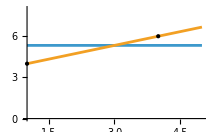

```mathematica
linePlot=Plot[{averageOverRangeOfInterest,line[x]},{x,xInitial,xFinal},PlotRange->{{xInitial,xFinal},{0,8}}];
p1={x1,y1};
p2={x2,y2};
pointPlot=Graphics[Point[{p1,p2}]];
Show[{linePlot,pointPlot}]
```

### General Case

Having done a little example of (a) getting a line from two points, (x_1,y_1) and (x_2,y_2),  and then (b) computing the average value of this line over a range of interest, we can do it fully generally. The line obeys:

y(x)=(y_2-y_1)/(x_2-x_1)(x-x_1)+y_1

A trapezoid approximation is a perfect estimate of a line’s average, so we just evaluate y(x) at x_i and x_f and compute the average:

y_avg=((y_2-y_1)/(x_2-x_1)(x_i-x_1)+y_1+(y_2-y_1)/(x_2-x_1)(x_f-x_1)+y_1)/2

We have a nice simplification if we choose x_1=x_i, which is in-line with what second-order Runge-Kutta does:

y_avg=(y_1+(y_2-y_1)/(x_2-x_i)(x_f-x_i)+y_1)/2

Also, if we rewrite x_2=x_i+α (x_f-x_i), we get lots more simplification:

y_avg=(y_1+(y_2-y_1)/(x_i+α (x_f-x_i)-x_i)(x_f-x_i)+y_1)/2=y_1+(y_2-y_1)/(2α)=(1-1/(2α))y_1+1/(2α)y_2

### Application to General Runge-Kutta 2

This is exactly what was claimed to be the best estimate of the average when we did General Second-Order Runge-Kutta.

Just put in for y_1 the value of a(t_i,x(t_i),v(t_i)), and for y_i the value of a(t^*,x^*,v^*).

You get the best estimate of a_avg that you can get with only two evaluations of a:

a_avg=(1-1/(2α))a(t_i,x(t_i),v(t_i))+1/(2α)a(t^*,x^*,v^*)

Our standard special cases are α=1/2 which gives midpoint, and α=1 which gives a trapezoid.